```mathematica
a=0.5292;
Z=1;
```

```mathematica
Clear[Φ]; 
Φ[n_Integer,ℓ_Integer][ρ_]:=Module[{const},
const=Sqrt[((n-ℓ-1)!)/((n+ℓ)! 2 n)];
const (2 Z ρ/n)^ℓ  LaguerreL[n-ℓ-1,2 ℓ+1,(2 Z ρ)/n] Exp[-(Z ρ)/n]];
```

```mathematica
Clear[R];
R[n_,ℓ_][r_]:=(2Z/ (n a))^(3/2) Φ[n,ℓ][r/a];
```

```mathematica
Unprotect[s];
s=.
s[r_,θ_,ϕ_][n_]:=Module[{},
R[n,0][r]* SphericalHarmonicY[0,0,θ,ϕ]];
Protect[s];
```

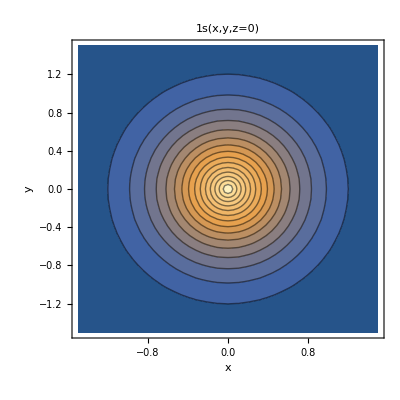

```mathematica
convCarts={ r->Sqrt[x^2+y^2+z^2]};

ContourPlot[Evaluate[(s[r,θ,ϕ][5]/.convCarts)/.z->0],{x,-1.5,1.5},{y,-1.5,1.5}, Contours->15,PlotRange->All,FrameLabel->{"x","y"}, PlotLabel->"1s(x,y,z=0)"]
```

```mathematica
Manipulate[ContourPlot3D[Evaluate[(s[r,θ,ϕ][nn]==0.1/.convCarts)],{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.5,1.5}, Contours->10,PlotRange->All, PlotLabel->"1s(x,y,z=0)"],{nn,1,5,1},ControlType->PopupMenu]
```